```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0 && Element[k,Integers] && k>0
```

r>0&&m∈Integers&&n∈Integers&&s>0&&k∈Integers&&k>0

```mathematica
m=2;
```

```mathematica
f[r_,En_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}}-0*IdentityMatrix[2]*I*r^p;f[r,En]//MatrixForm
```

(1/r | ⅈ (En-r^2)
ⅈ (En-r^2) | -2/r)

```mathematica
En=.;n=.
```

```mathematica
fE=D[f[r,En],En]
```

{{0,ⅈ},{ⅈ,0}}

```mathematica
u={a[n]*x^(2*n),b[n]*x^(2*n+1)}*x^s
```

{x^209 a[100],x^210 b[100]}

```mathematica
p=2;
```

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[(D[u,x]-r'[x]*f[r[x]].u)*x^(-s+1)]]],{x^n,a[n],b[n]}];
g1//MatrixForm
```

(x^(2 n) ((1-m+2 n+s) a[n]+(-ⅈ En x^2+ⅈ x^4) b[n])
x^(2 n) ((-ⅈ En x+ⅈ x^3) a[n]+(x+m x+2 n x+s x) b[n]))

```mathematica
s=-1+m;
```

```mathematica
g2=Table[Simplify[Sum[D[g1,{x,n2}]/n2!,{n,0,10}]/.x->0],{n2,0,10}];g2//MatrixForm
```

(0 | 0
0 | -ⅈ En a[0]+2 m b[0]
2 a[1]-ⅈ En b[0] | 0
0 | ⅈ a[0]-ⅈ En a[1]+2 (1+m) b[1]
4 a[2]+ⅈ (b[0]-En b[1]) | 0
0 | ⅈ a[1]-ⅈ En a[2]+2 (2+m) b[2]
6 a[3]+ⅈ (b[1]-En b[2]) | 0
0 | ⅈ a[2]-ⅈ En a[3]+2 (3+m) b[3]
8 a[4]+ⅈ (b[2]-En b[3]) | 0
0 | ⅈ a[3]-ⅈ En a[4]+2 (4+m) b[4]
10 a[5]+ⅈ (b[3]-En b[4]) | 0)

```mathematica
a[0]=1; b[0]=ⅈ En a[0]/2/m;a[1]=ⅈ En b[0]/2;
```

```mathematica
a[0]=1; b[0]=ⅈ En a[0]/2/m;a[1]=ⅈ En b[0]/2;
b[n_]:=I*(En*a[n]-a[n-1])/2/(n+m);
a[n_]:=Simplify[I*(En b[n-1]-b[n-2])/2/n]
```

```mathematica
a[1]
```

-En^2/8

```mathematica
m=2;
```

```mathematica
En=.
```

```mathematica
Un[En_,m_,nN_,x_]:=Module[{n,U},
U={1};AppendTo[U,-En^2/(4 m)];AppendTo[U,(En (4+En^3+8 m))/(32 m (1+m))];G={ⅈ En /2/m};

For[n=3,n<nN,n++,
AppendTo[U,-((-1+m+n) U[[-2+n]]+En ((3-2 m-2 n) U[[-1+n]]+En (-2+m+n)U[[n]]))/(4 n (-2+m+n) (-1+m+n))];
];
({1,ⅈ En /2/m*x}+Sum[{U[[n+1]]*x^(2*n),I*(En*U[[n+1]]-U[[n]])/2/(n+m)*x^(2*n+1)},{n,1,nN-1} ])*x^(-1+m)//N]
```

```mathematica
U[En_,m_,g_,X_]:=Module[{n=10,U,G},
U=Un[En,m,n,X];G=-Un[En,m,n+1,X];
While[Sqrt[Abs[Conjugate[U-G].(U-G)]]>g,
n++;
U=G;G=-Un[En,m,n+1,X];

];
{Un[En,m,n,X],n}]
```

```mathematica
Ener[Ene_]:=Module[{U1,U2,U1S,U2S,VV={{0,1},{-1,0}},En,Enn,NN,Erg,kE,k,n,m,r,h},
En=Ene;
Label[begin];
n=3500;
m=2;
r=17//N;h=-16.9/n;
k={1,-1};
kE={0,0};
Do[
k0=h*f[r,En].k;k1=h*f[r+h/2,En].(k+k0/2);k2=h*f[r+h/2,En].(k+k1/2);k3=h*f[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);

k0=h*(fE.k+f[r,En].kE);k1=h*(fE.k+f[r+h/2,En].(kE+k0/2));k2=h*(fE.k+f[r+h/2,En].(kE+k1/2));k3=h*(fE.k+f[r+h,En].(kE+k2));
kE+=1/6*(k0+2*k1+2*k2+k3);

r+=h;

,{n}];

NN=U[En,m,10^-10,r][[2]];

{U1,U2}=Un[En,m,NN,r];
{U1S,U2S}=D[Un[Enn,m,NN,r],Enn]/.Enn->En;

Erg=k[[1]]*U2-U1*k[[2]];

If[Abs[Erg/U2/k[[2]]]>0.06,
En-=Erg/(U2S k⟦1⟧-U1S k⟦2⟧+U2 kE⟦1⟧-U1 kE⟦2⟧);
(*Print[{En,Erg/U2/k[[2]]}];*)Goto[begin];
 ];
{En,Erg/U2/k[[2]]}
]
```

```mathematica
For[i=0,i<10,i+=0.1,Sepp=Ener[i];Print[{i,Sepp}];AppendTo[Energie,{i,Sepp}];]
```

```mathematica
Ener[3.8]
```

{3.61902+0.265337 ⅈ,-0.00109633-0.000496109 ⅈ}

```mathematica
Energie//MatrixForm
```

(0 | {-0.0348248+0.273429 ⅈ,0.0824271+0.00377436 ⅈ}
0.1 | {-0.0348248+0.273429 ⅈ,0.0214202-0.0233512 ⅈ}
0.2 | {0.161054+0.274461 ⅈ,-0.00191844+0.059646 ⅈ}
0.3 | {0.161054+0.274461 ⅈ,0.0430159+0.0247969 ⅈ}
0.4 | {0.357691+0.275498 ⅈ,-0.0239546+0.0157214 ⅈ}
0.5 | {0.357691+0.275498 ⅈ,0.0119417+0.0477695 ⅈ}
0.6 | {0.555088+0.276533 ⅈ,-0.0148071+0.000774966 ⅈ}
0.7 | {0.555088+0.276533 ⅈ,-0.00890224+0.0489729 ⅈ}
0.8 | {0.753241+0.277561 ⅈ,-0.00846342-0.00200356 ⅈ}
0.9 | {0.753241+0.277561 ⅈ,-0.0231779+0.047652 ⅈ}
1. | {0.952144+0.278576 ⅈ,0.0783007+0.0337232 ⅈ}
1.1 | {0.952144+0.278576 ⅈ,-0.0355808+0.0442028 ⅈ}
1.2 | {1.15178+0.279569 ⅈ,0.0505876+0.0270738 ⅈ}
1.3 | {1.15178+0.279569 ⅈ,-0.045905+0.0363295 ⅈ}
1.4 | {1.35215+0.280534 ⅈ,0.03465+0.019346 ⅈ}
1.5 | {1.35215+0.280534 ⅈ,-0.0511494+0.0227949 ⅈ}
1.6 | {1.55321+0.281461 ⅈ,0.0245336+0.0125636 ⅈ}
1.7 | {1.55321+0.281461 ⅈ,-0.0479442+0.00618525 ⅈ}
1.8 | {1.75494+0.282337 ⅈ,0.0174311+0.00717699 ⅈ}
1.9 | {1.75494+0.282337 ⅈ,-0.0358656-0.00734238 ⅈ}
2. | {1.9573+0.283143 ⅈ,0.0119518+0.00328444 ⅈ}
2.1 | {1.9573+0.283143 ⅈ,-0.0202808-0.0123854 ⅈ}
2.2 | {2.16024+0.283843 ⅈ,0.00759541+0.000846598 ⅈ}
2.3 | {2.16024+0.283843 ⅈ,-0.00901651-0.00938155 ⅈ}
2.4 | {2.36368+0.284381 ⅈ,-0.0649912+0.00531311 ⅈ}
2.5 | {2.36368+0.284381 ⅈ,-0.00765636-0.00670322 ⅈ}
2.6 | {2.56752+0.284638 ⅈ,-0.0300368+0.00916306 ⅈ}
2.7 | {2.56752+0.284638 ⅈ,0.017086+0.00489736 ⅈ}
2.8 | {2.7716+0.284365 ⅈ,-0.0102766+0.00631036 ⅈ}
2.9 | {2.7716+0.284365 ⅈ,0.00255367-0.007645 ⅈ}
3. | {2.97573+0.282951 ⅈ,0.0324564-0.0390568 ⅈ}
3.1 | {2.97573+0.282951 ⅈ,-0.0129679+0.0493867 ⅈ}
3.2 | {3.18002+0.278733 ⅈ,0.00561139-0.0124434 ⅈ}
3.3 | {3.38843+0.267181 ⅈ,-0.00706132-0.00222546 ⅈ}
3.4 | {3.38843+0.267181 ⅈ,0.0716424+0.0146798 ⅈ}
3.5 | {3.51788+0.111334 ⅈ,0.00243169+0.000403973 ⅈ}
3.6 | {3.51788+0.111334 ⅈ,-0.0000168755+0.000409094 ⅈ}
3.7 | {3.51788+0.111334 ⅈ,0.0000574665-0.000997058 ⅈ}
3.8 | {3.61902+0.265337 ⅈ,0.0159846+0.00559245 ⅈ}
3.9 | {3.83002+0.279236 ⅈ,-0.00334078-0.00754872 ⅈ}
4. | {3.83002+0.279236 ⅈ,-0.0031197-0.0264905 ⅈ}
4.1 | {4.03602+0.284821 ⅈ,0.0202834+0.030361 ⅈ}
4.2 | {4.03602+0.284821 ⅈ,0.00672479-0.00922651 ⅈ}
4.3 | {4.24235+0.286678 ⅈ,0.011193+0.00918883 ⅈ}
4.4 | {4.03602+0.284821 ⅈ,0.00496042+0.0116323 ⅈ}
4.5 | {4.44907+0.286035 ⅈ,-0.0699411-0.0157006 ⅈ}
4.6 | {4.65592+0.281786 ⅈ,-0.0128516+0.0066142 ⅈ}
4.7 | {4.65592+0.281786 ⅈ,-0.0326016+0.0063652 ⅈ}
4.8 | {4.8653+0.268593 ⅈ,-0.00101728+0.00822936 ⅈ}
4.9 | {4.8653+0.268593 ⅈ,0.0328955+0.00350871 ⅈ}
5. | {5.02602+0.142922 ⅈ,0.00271581+0.0632135 ⅈ}
5.1 | {5.02603+0.142926 ⅈ,-0.000932623-0.000541224 ⅈ}
5.2 | {5.32464+0.279517 ⅈ,-0.00715488+0.00675674 ⅈ}
5.3 | {5.10897+0.258743 ⅈ,0.0175854-0.0479305 ⅈ}
5.4 | {5.32464+0.279518 ⅈ,0.000118089+0.0186131 ⅈ}
5.5 | {5.32464+0.279517 ⅈ,0.00924017-0.00980417 ⅈ}
5.6 | {5.53302+0.286516 ⅈ,-0.0380211-0.0675122 ⅈ}
5.7 | {5.32464+0.279518 ⅈ,0.0105739+0.015473 ⅈ}
5.8 | {5.74162+0.287838 ⅈ,-0.0199566-0.0134933 ⅈ}
5.9 | {5.95051+0.284332 ⅈ,-0.0354819-0.0250697 ⅈ}
6. | {5.95051+0.284332 ⅈ,-0.00913623-0.00047985 ⅈ}
6.1 | {6.16131+0.271158 ⅈ,0.0252866-0.0560522 ⅈ}
6.2 | {6.16131+0.271152 ⅈ,0.0101888+0.0123834 ⅈ}
6.3 | {6.33701+0.158456 ⅈ,-0.00105735-0.000319741 ⅈ}
6.4 | {6.33701+0.158456 ⅈ,-0.000671294+0.00110609 ⅈ}
6.5 | {5.53302+0.286517 ⅈ,-0.0310481-0.0398119 ⅈ}
6.6 | {6.41235+0.255483 ⅈ,0.0235597-0.0317144 ⅈ}
6.7 | {6.63113+0.280631 ⅈ,0.00382499+0.00786223 ⅈ}
6.8 | {6.63113+0.280631 ⅈ,-0.0077521+0.00818432 ⅈ}
6.9 | {6.84154+0.287981 ⅈ,-0.022262-0.0132369 ⅈ}
7. | {6.84154+0.287983 ⅈ,0.00101079-0.0076893 ⅈ}
7.1 | {7.05207+0.28802 ⅈ,-0.00646432-0.000525755 ⅈ}
7.2 | {7.26328+0.28014 ⅈ,-0.00507427+0.00750115 ⅈ}
7.3 | {7.26327+0.280144 ⅈ,0.0673018+0.00510217 ⅈ}
7.4 | {7.48771+0.249352 ⅈ,-0.0063826-0.00716244 ⅈ}
7.5 | {7.53947+0.171252 ⅈ,0.00125585+0.00522793 ⅈ}
7.6 | {7.53948+0.171245 ⅈ,-0.0014772+0.00081522 ⅈ}
7.7 | {7.53949+0.171252 ⅈ,0.00201748-0.00137817 ⅈ}
7.8 | {7.74042+0.275795 ⅈ,0.0535+0.0351612 ⅈ}
7.9 | {7.74041+0.27578 ⅈ,0.0102428-0.0180593 ⅈ}
8. | {7.9533+0.287735 ⅈ,-0.0215442+0.012056 ⅈ}
8.1 | {7.95331+0.287745 ⅈ,0.0599208-0.0229489 ⅈ}
8.2 | {8.16549+0.289055 ⅈ,0.0735446-0.0426555 ⅈ}
8.3 | {8.16548+0.289041 ⅈ,0.00452665+0.0332604 ⅈ}
8.4 | {8.37849+0.280812 ⅈ,0.0165815-0.0119099 ⅈ}
8.5 | {8.6095+0.244542 ⅈ,-0.0122388-0.000407866 ⅈ}
8.6 | {8.64233+0.181294 ⅈ,0.00614591+0.00163093 ⅈ}
8.7 | {8.64232+0.181244 ⅈ,-0.0052266+0.00204766 ⅈ}
8.8 | {8.64234+0.181016 ⅈ,-0.0559045-0.00772336 ⅈ}
8.9 | {8.86137+0.278848 ⅈ,0.0378659+0.0469596 ⅈ}
9. | {8.86138+0.27881 ⅈ,-0.00298264-0.0446443 ⅈ}
9.1 | {9.07571+0.289363 ⅈ,0.0192018-0.00629468 ⅈ}
9.2 | {9.0757+0.289343 ⅈ,-0.0655082+0.0448379 ⅈ}
9.3 | {9.28963+0.288376 ⅈ,0.00576278-0.0502462 ⅈ}
9.4 | {9.28962+0.288357 ⅈ,-0.0151671+0.0315395 ⅈ}
9.5 | {9.50588+0.273435 ⅈ,-0.000351129-0.0116833 ⅈ}
9.6 | {9.66759+0.171037 ⅈ,-0.0194593+0.0666014 ⅈ}
9.7 | {9.66791+0.171195 ⅈ,-0.00189307-0.00197333 ⅈ}
9.8 | {9.66789+0.171216 ⅈ,0.00293916+0.0000546853 ⅈ}
9.9 | {9.77232+0.262805 ⅈ,-0.00545773+0.017099 ⅈ})

```mathematica
Energien={Im[#[[2,1]]],Re[#[[2,1]]]}&/@Energie;
```

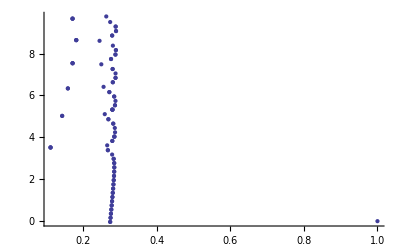

```mathematica
ListPlot[Append[Energien,{1,0}],AxesOrigin->{0,0},PlotRange->All]
```

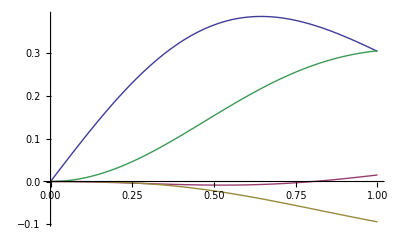

```mathematica
G={Re[#],Im[#]}&[Un[Energie[[1]],2,15,x]];Plot[G,{x,0,1},PlotRange->All]
```

```mathematica
En=Energie[[1]];n=3500;
m=2;
r=17//N;h=-16.9/n;
k={1,-1};kK={{r,k}};
Do[
k0=h*f[r,En].k;k1=h*f[r+h/2,En].(k+k0/2);k2=h*f[r+h/2,En].(k+k1/2);k3=h*f[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[kK,{r,k}],{n}];En=.
```

```mathematica
k/k[[1]]-Un[Energie[[1]],2,20,0.1]/Un[Energie[[1]],2,20,0.1][[1]]
```

{0.+7.92188×10^-19 ⅈ,0.0000440082+0.0000213747 ⅈ}

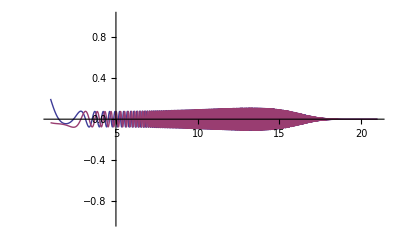

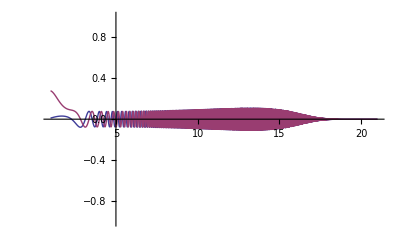

```mathematica
n=6000;S=1;h=20/n;ra=1;En=3.517884643304668+0.11133398841863644ⅈ;m=2;r=1;k=U[En,m,10^-10,r][[1]];
kK={{r,k}};
Do[
k0=h*f[r,En].k;k1=h*f[r+h/2,En].(k+k0/2);k2=h*f[r+h/2,En].(k+k1/2);k3=h*f[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[kK,{r,k}],{n}];

ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,1]]]}&/@kK[[S;;n]]//N}],PlotRange->{-ra,ra},Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;n]]//N}],PlotRange->{-ra,ra},Joined->True]
En=.;r=.;
```

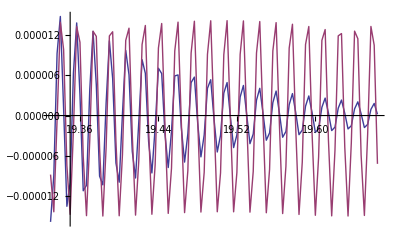

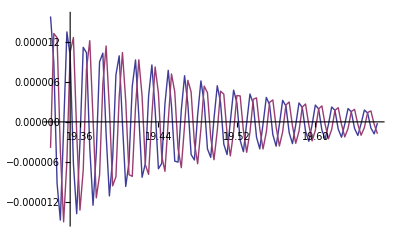

```mathematica
S=5500;n=100;ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;S+n]]//N},{ {#[[1]],0.000015*Cos[#[[1]]^3/3-#[[1]]*Re[3.517884613174765]]}&/@kK[[S;;S+n]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;S+n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;S+n]]//N}],PlotRange->All,Joined->True]
```

```mathematica
Exp[I*Im[Energie[[1]]]*x]
```

ⅇ^(0.278733 ⅈ x)